```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,ϕ,θp,ϕp,kp,cq,vf,B,μ,fac,βintra} ∈ Reals && k>0 && kf>0 &&  0<=θ<=π && 0<=θp<=π && βintra>0 &&  vf>0;
rep={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
rep1={kx->Subscript[k, x],ky->Subscript[k, y],kz->Subscript[k, z],θ->γ,θp->γ^p,Bz->Subscript[B, z],vf->Subscript[v, 0]};
```

## phys quantities

```mathematica
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,ϕ,θp,ϕp,kp,vinter,vinter} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && vintra>0 && vinter>0;
en0=vf √(kx^2+ky^2+kz^2);
Print["band vel."];
v0=FullSimplify[Grad[en0,{kx,ky,kz}]/.rep,ass]
Print["v0.k"];
v0dotk=FullSimplify[v0.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["BC vector"];
Ω(* {(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)}*)=(χ kz)/((kx^2+ky^2+kz^2)^2){ kx ,ky ,kz};FullSimplify[Ω/.rep,ass]
ommvec=(-e vf kz χ)/(2(kx^2+ky^2+kz^2)^(3/2)){  kx,ky,kz};
Print["OMM energy"];
enom=-ommvec.{0,0,Bz};
FullSimplify[enom/.rep,ass]
Print["OMM correc. to band vel."];
vm=FullSimplify[Grad[enom,{kx,ky,kz}],ass]
FullSimplify[vm/.rep,ass]
Print["vm.k"];
vmdotk=FullSimplify[vm.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["v.k"];
vdotk=FullSimplify[(v0+vm).{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["v.Ω"];
FullSimplify[(v0+vm).Ω/.rep,Assumptions->k ∈ Reals && k>0]
```

band vel.

{vf Cos[ϕ] Sin[θ],vf Sin[θ] Sin[ϕ],vf Cos[θ]}

v0.k

k vf

BC vector

{(χ Cos[θ] Cos[ϕ] Sin[θ])/k^2,(χ Cos[θ] Sin[θ] Sin[ϕ])/k^2,(χ Cos[θ]^2)/k^2}

OMM energy

(Bz e vf χ Cos[θ]^2)/(2 k)

OMM correc. to band vel.

{-(3 Bz e kx kz^2 vf χ)/(2 (kx^2+ky^2+kz^2)^(5/2)),-(3 Bz e ky kz^2 vf χ)/(2 (kx^2+ky^2+kz^2)^(5/2)),(Bz e kz (2 (kx^2+ky^2)-kz^2) vf χ)/(2 (kx^2+ky^2+kz^2)^(5/2))}

{-(3 Bz e vf χ Cos[θ]^2 Cos[ϕ] Sin[θ])/(2 k^2),-(3 Bz e vf χ Cos[θ]^2 Sin[θ] Sin[ϕ])/(2 k^2),-(Bz e vf χ (Cos[θ]+3 Cos[3 θ]))/(8 k^2)}

vm.k

-(Bz e vf χ Cos[θ]^2)/(2 k)

v.k

-(vf (-4 k^2+Bz e χ+Bz e χ Cos[2 θ]))/(4 k)

v.Ω

-(vf χ Cos[θ] (-4 k^2+Bz e χ+Bz e χ Cos[2 θ]))/(4 k^4)

## Fermi surface

```mathematica
FullSimplify[Flatten[SolveValues[vf kf+(Bz e kf vf Cos[θ]^2)/2==μ,kf],1],ass]
```

{(2 μ)/(2 vf+Bz e vf Cos[θ]^2)}

## Matrix forms

```mathematica
Clear[G];(* -Graphics-*)
G=(3+4ct ctp+c2t c2tp)/8;
```

```mathematica
Clear[v1,v2,v3,ξ];v1[ξ_,θ_,ϕ_]={-ⅈ/(√2),(-ξ ⅈ ⅇ^(-ξ ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)};
v2[ξ_]={ⅈ/(√2),(-ξ ⅈ ⅇ^(-ξ ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)};
v3[ξ_]={0,ξ ⅈ ⅇ^(-ξ ⅈ ϕ) Cos[θ],Sin[θ]};
v1dag[ξ_,θ_,ϕ_]={ⅈ/(√2),(ξ ⅈ ⅇ^(ξ ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)};
amptot=(FullSimplify[Integrate[((v1dag[ξp,θp,ϕp].v1[ξ,θ,ϕ])(v1dag[ξ,θ,ϕ].v1[ξp,θp,ϕp]))/(2π),{ϕp,0,2π}],ass]/.{ξ^2 ->1,ξp^2->1})/.{(-1+ⅇ^(2 ⅈ π ξp))->2,Sin[π ξp]->0}
```

1/4 ((1+Cos[θ] Cos[θp])^2+Sin[θ]^2 Sin[θp]^2)

```mathematica
1+ⅇ^(2 ⅈ π ξp)/.ξp->-1
```

2

```mathematica
amp=FullSimplify[Integrate[((vec1dag[θ,ϕ].vec1[θp,ϕp])(vec1dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
amp2=FullSimplify[Integrate[((vect1dag[θ,ϕ].vect1[θp,ϕp])(vect1dag[θp,ϕp].vect1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
ampmix1=FullSimplify[Integrate[((vect1dag[θ,ϕ].vec1[θp,ϕp])(vec1dag[θp,ϕp].vect1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
ampmix2=FullSimplify[Integrate[((vec1dag[θ,ϕ].vect1[θp,ϕp])(vect1dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])

1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])

1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])

«1 more identical outputs»

```mathematica
1/4 ((1+Cos[θ] Cos[θp])^2+Sin[θ]^2 Sin[θp]^2)==1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])//FullSimplify
```

True

```mathematica
((1+Cos[θ] Cos[θp])^2+(1-Cos[θ]^2 )(1-Cos[θp]^2 ))/4//Expand//FullSimplify
```

1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])

```mathematica
FullSimplify[(Cos[2 θ] Cos[2 θp]//TrigExpand)/.{Cos[θ]^2->cg^2,Cos[θp]^2->cgp^2,Sin[θ]^2->1-cg^2,Sin[θp]^2->1-cgp^2}]
3+4 cg cgp+%//Expand
```

(-1+2 cg^2) (-1+2 cgp^2)

4-2 cg^2+4 cg cgp-2 cgp^2+4 cg^2 cgp^2

```mathematica
Clear[G,eq,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
Clear[G];
G=1/8 (3+4 ct ctp+c2t  c2tp);
Λ1byτ=λ1-h1+a1 ct+b1 c2t;
Λ2byτ=λ2-h2+a2 ct+b2 c2t;
lhs1=Λ1byτ+h1;
lhs2=Λ2byτ+h2;    

rhs1=xintθpf1  βintra G(λ1-h1+a1 ctp+b1 c2tp)+βinter  xintθpf2 G(λ2-h2+a2 ctp+b2 c2tp);

rhs2=xintθpf2 βintra   G(λ2-h2+a2 ctp+b2 c2tp)+βinter  xintθpf1 G (λ1-h1+a1 ctp+b1 c2tp);

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0},{c2t,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct,0,1},{c2t,0,0}]//FullSimplify;
eqn3=SeriesCoefficient[eq,{ct,0,0},{c2t,0,1}]//FullSimplify;
eqn1+ct eqn2+c2t eqn3==eq //FullSimplify
(************)
eq=lhs2-rhs2;
eqn4=SeriesCoefficient[eq,{ct,0,0},{c2t,0,0}]//FullSimplify;
eqn5=SeriesCoefficient[eq,{ct,0,1},{st,0,0}]//FullSimplify;
eqn6=SeriesCoefficient[eq,{c2,0,0},{c2t,0,1}]//FullSimplify;

eqn4+ct eqn5+c2t eqn6==eq //FullSimplify
```

True

True

```mathematica
Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0,eqn5==0,eqn6==0},{λ1,a1,b1,λ2,a2,b2}];
array=(Normal[arr]//FullSimplify)/.{ct->cg,ctp->cg,c2t->c2g,c2tp->c2g};
cmat1=array[[1]]//Expand;
cmat2=array[[2]]//Expand;
Dimensions[cmat2]
rep1={c2g cg xintθpf1 ->c2gcg1,c2g^2 xintθpf1->c2gc2g1,cg^2 xintθpf1->cgcg1, cg h1 xintθpf1 -> hcg1,c2g h1 xintθpf1 -> hc2g1,h1 xintθpf1 ->hunity1,c2g xintθpf1->c2g1,cg xintθpf1->cg1, xintθpf1  ->unity1(*%%%%%%*),c2g cg xintθpf2 ->c2gcg2,c2g^2 xintθpf2->c2gc2g2,cg^2 xintθpf2->cgcg2, cg h2 xintθpf2 -> hcg2,c2g h2 xintθpf2 -> hc2g2,h2 xintθpf2 ->hunity2,c2g xintθpf2->c2g2,cg xintθpf2->cg2, xintθpf2  ->unity2};
MatrixForm[cmat2];
MatrixForm[cmat2/.rep1]
MatrixForm[cmat1];
MatrixForm[cmat1/.rep1]
```

{6,6}

(1-(3 unity1 βintra)/8 | -(3 cg1 βintra)/8 | -(3 c2g1 βintra)/8 | -(3 unity2 βinter)/8 | -(3 cg2 βinter)/8 | -(3 c2g2 βinter)/8
-(cg1 βintra)/2 | 1-(cgcg1 βintra)/2 | -(c2gcg1 βintra)/2 | -(cg2 βinter)/2 | -(cgcg2 βinter)/2 | -(c2gcg2 βinter)/2
-(c2g1 βintra)/8 | -(c2gcg1 βintra)/8 | 1-(c2gc2g1 βintra)/8 | -(c2g2 βinter)/8 | -(c2gcg2 βinter)/8 | -(c2gc2g2 βinter)/8
-(3 unity1 βinter)/8 | -(3 cg1 βinter)/8 | -(3 c2g1 βinter)/8 | 1-(3 unity2 βintra)/8 | -(3 cg2 βintra)/8 | -(3 c2g2 βintra)/8
-(cg1 βinter)/2 | -(cgcg1 βinter)/2 | -(c2gcg1 βinter)/2 | -(cg2 βintra)/2 | 1-(cgcg2 βintra)/2 | -(c2gcg2 βintra)/2
-(c2g1 βinter)/8 | -(c2gcg1 βinter)/8 | -(c2gc2g1 βinter)/8 | -(c2g2 βintra)/8 | -(c2gcg2 βintra)/8 | 1-(c2gc2g2 βintra)/8)

((3 hunity2 βinter)/8+(3 hunity1 βintra)/8
(hcg2 βinter)/2+(hcg1 βintra)/2
(hc2g2 βinter)/8+(hc2g1 βintra)/8
(3 hunity1 βinter)/8+(3 hunity2 βintra)/8
(hcg1 βinter)/2+(hcg2 βintra)/2
(hc2g1 βinter)/8+(hc2g2 βintra)/8)

```mathematica
Clear[arr,array,cmat];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0},{λ1,a1,b1}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
rep={intθpf1->af1,c2tp->c2t,ctp->ct};
cmat=Expand[cmat/.rep];
array[[1]]=Expand[array[[1]]/.rep];
MatrixForm[cmat]//FullSimplify
MatrixForm[array[[1]]]//FullSimplify
```

(1-(3 xintθpf1 βintra)/8 | -3/8 ct xintθpf1 βintra | -3/8 c2t xintθpf1 βintra
-1/2 ct xintθpf1 βintra | 1-1/2 ct^2 xintθpf1 βintra | -1/2 c2t ct xintθpf1 βintra
-1/8 c2t xintθpf1 βintra | -1/8 c2t ct xintθpf1 βintra | 1-1/8 c2t^2 xintθpf1 βintra)

(-3/8 (-h1 xintθpf1 βintra+xintθpf2 βinter (b2 c2t+a2 ct-h2+λ2))
-1/2 ct (-h1 xintθpf1 βintra+xintθpf2 βinter (b2 c2t+a2 ct-h2+λ2))
-1/8 c2t (-h1 xintθpf1 βintra+xintθpf2 βinter (b2 c2t+a2 ct-h2+λ2)))

```mathematica
(* ({{1-3 zero β, -3 ct β, -3 c2t β}, {-4 ct β, 1-4 af1 ctsq β, -4 ctc2t β}, {-c2t β, -af1 ctc2t β, 1-af1 c2tsq β}}) and  β({{3 hzero}, {4 hct}, {hc2t}})*)
```

## sigma

```mathematica
Clear[sig];
sig[B_,μ_,v0_,{βinter_,βintra_}]:=Block[{e=1,BCvec1,BCvec2,v0vec,vf=v0,χ,vmvec1,vmvec2,matr,θ,τ1,kf1,f1,vdotk1,τ2,kf2,f2,vdotk2,cs,λ1,a1,b1,λ2,a2,b2,θp,ϕ,Dphase1,Dphase2,h1,h2,hunity1,hunity2,hcg1,hcg2,hc2g1,hc2g2,unity1,unity2,cg1,c2g1,cg2,c2g2,cgcg1,cgcg2,c2gc2g1,c2gc2g2,c2gcg1,c2gcg2,colvec,mat,sol,Λ1,s1,int1,Λ2,s2,int2,cs1,cs2,u1,u2,c1,c2,c21,c22,rvec},
χ=1;
kf1[θ_]=(μ+√(μ^2-2χ  B e vf vf Cos[θ]^2))/(2 vf) ;
BCvec1[θ_]=χ Cos[θ]/kf1[θ]^2{ Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
Dphase1[θ_]=1 +e  B(BCvec1[θ])[[3]] ;
v0vec[θ_]=vf{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ], Cos[θ]};
(* {-(3 Bz e vf χ Cos[θ]^2 Cos[ϕ] Sin[θ])/(2 k^2),-(3 Bz e vf χ Cos[θ]^2 Sin[θ] Sin[ϕ])/(2 k^2),-(Bz e vf χ (Cos[θ]+3 Cos[3 θ]))/(8 k^2)} *)
vmvec1[θ_]=(-χ vf  e B)/(2 kf1[θ]^2){ 3  Cos[θ]^2 Cos[ϕ] Sin[θ],3 Cos[θ]^2 Sin[θ] Sin[ϕ],(Cos[θ]+3 Cos[3 θ])/4};
vdotk1[θ_]=kf1[θ] vf-(χ e B vf Cos[θ]^2)/(2 kf1[θ]);(* -(Bz e vf χ Cos[θ]^2)/(2 k)*)
h1[θ_]=1/Dphase1[θ]((**)(v0vec[θ]+vmvec1[θ])[[3]]-e B (χ vf Cos[θ] (χ B e-4 kf1[θ]^2 +χ B e Cos[2 θ]))/(4 kf1[θ]^4)(**));(*-(vf χ Cos[θ] (-4 k^2+Bz e χ+Bz e χ Cos[2 θ]))/(4 k^4) *)
(*****************)
χ=-1;
kf2[θ_]= (μ+√(μ^2-2χ  vf vf e B Cos[θ]^2))/(2 vf) ;
BCvec2[θ_]=χ Cos[θ]/kf2[θ]^2{ Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
Dphase2[θ_]=1 +e  B(BCvec2[θ])[[3]] ;
vmvec2[θ_]=(-χ vf  e B)/(2 kf2[θ]^2){ 3  Cos[θ]^2 Cos[ϕ] Sin[θ],3 Cos[θ]^2 Sin[θ] Sin[ϕ], (Cos[θ]+3 Cos[3 θ])/4};
vdotk2[θ_]=kf2[θ] vf-(χ e B vf Cos[θ]^2)/(2 kf2[θ]);
h2[θ_]=1/Dphase2[θ]((**)(v0vec[θ]+vmvec2[θ])[[3]]-e B (χ vf Cos[θ] (χ B e-4 kf2[θ]^2 +χ B e Cos[2 θ]))/(4 kf2[θ]^4))(**);
(***********************)
τ1[θ_]=(1/8 3βintra Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]]+
1/8 4βintra Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]]+1/8 βintra Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[2θp],{θp,0,π}]]+1/8 3βinter Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]]+
1/8 4βinter Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]]+1/8 βinter Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[2θp],{θp,0,π}]])^-1;
(*******************)
τ2[θ_]=(1/8 3βintra Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]]+
1/8 4βintra Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]]+1/8 βintra Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[2θp],{θp,0,π}]]+1/8 3βinter Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]]+
1/8 4βinter Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]]+1/8 βinter Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[2θp],{θp,0,π}]])^-1;
(*****************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
unity1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
cg1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
cgcg1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
c2g1=Quiet[NIntegrate [f1[θp] Cos[2θp],{θp,0,π}]];
c2gc2g1=Quiet[NIntegrate [f1[θp] Cos[2θp]^2,{θp,0,π}]];
c2gcg1=Quiet[NIntegrate [f1[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hunity1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hcg1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hc2g1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[2θp],{θp,0,π}]];
(***************)
unity2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
cg2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
cgcg2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
c2g2=Quiet[NIntegrate [f2[θp] Cos[2θp],{θp,0,π}]];
c2gc2g2=Quiet[NIntegrate [f2[θp] Cos[2θp]^2,{θp,0,π}]];
c2gcg2=Quiet[NIntegrate [f2[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hunity2=Quiet[NIntegrate [f2[θp] h2[θp],{θp,0,π}]];
hcg2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hc2g2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[2θp],{θp,0,π}]];
colvec=({{(3 hunity2 βinter)/8+(3 hunity1 βintra)/8}, {(hcg2 βinter)/2+(hcg1 βintra)/2}, {(hc2g2 βinter)/8+(hc2g1 βintra)/8}, {(3 hunity1 βinter)/8+(3 hunity2 βintra)/8}, {(hcg1 βinter)/2+(hcg2 βintra)/2}, {(hc2g1 βinter)/8+(hc2g2 βintra)/8}});
mat=({{1-(3 unity1 βintra)/8, -(3 cg1 βintra)/8, -(3 c2g1 βintra)/8, -(3 unity2 βinter)/8, -(3 cg2 βinter)/8, -(3 c2g2 βinter)/8}, {-(cg1 βintra)/2, 1-(cgcg1 βintra)/2, -(c2gcg1 βintra)/2, -(cg2 βinter)/2, -(cgcg2 βinter)/2, -(c2gcg2 βinter)/2}, {-(c2g1 βintra)/8, -(c2gcg1 βintra)/8, 1-(c2gc2g1 βintra)/8, -(c2g2 βinter)/8, -(c2gcg2 βinter)/8, -(c2gc2g2 βinter)/8}, {-(3 unity1 βinter)/8, -(3 cg1 βinter)/8, -(3 c2g1 βinter)/8, 1-(3 unity2 βintra)/8, -(3 cg2 βintra)/8, -(3 c2g2 βintra)/8}, {-(cg1 βinter)/2, -(cgcg1 βinter)/2, -(c2gcg1 βinter)/2, -(cg2 βintra)/2, 1-(cgcg2 βintra)/2, -(c2gcg2 βintra)/2}, {-(c2g1 βinter)/8, -(c2gcg1 βinter)/8, -(c2gc2g1 βinter)/8, -(c2g2 βintra)/8, -(c2gcg2 βintra)/8, 1-(c2gc2g2 βintra)/8}});

matr=mat.{λ1,a1,b1,λ2,a2,b2};cs1=λ1 unity1-hunity1+a1 cg1+b1 c2g1;
cs2=λ2 unity2-hunity2+a2 cg2+b2 c2g2; cs=cs1+cs2;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,cs==0},{λ1,a1,b1,λ2,a2,b2}],1];
Λ1[θ_]=(-h1[θ]+λ1+a1 Cos[θ]+b1 Cos[2θ])/.sol;
Λ2[θ_]=(-h2[θ]+λ2+a2 Cos[θ]+b2 Cos[2θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];int2[θ_]=-f2[θ]h2[θ]Λ2[θ];

s1=Quiet[NIntegrate[int1[θ],{θ,0,π}]];s2=Quiet[NIntegrate[int2[θ],{θ,0,π}]];
(********* singularity of matrix ***********)
u1=Quiet[NIntegrate [f1[θp]/τ1[θp],{θp,0,π}]];
c1=Quiet[NIntegrate [f1[θp] Cos[θp]/τ1[θp],{θp,0,π}]];
c21=Quiet[NIntegrate [f2[θp] Cos[2θp]/τ2[θp],{θp,0,π}]];
u2=Quiet[NIntegrate [f2[θp]/τ2[θp],{θp,0,π}]];
c2=Quiet[NIntegrate [f2[θp] Cos[θp]/τ2[θp],{θp,0,π}]];
c22=Quiet[NIntegrate [f2[θp] Cos[2θp]/τ2[θp],{θp,0,π}]];

rvec={3/8 (βintra u1+βinter u2),1/2 (βintra c1+βinter c2),1/8 (βintra c21+βinter c22),3/8 (βintra u2+βinter u1),1/2 (βintra c2+βinter c1),1/8 (βintra c22+βinter c21)};
(*tau1[θ_]=(rvec[[1]]+rvec[[2]] Cos[θ]+rvec[[3]] Cos[2 θ])^-1;
tau2[θ_]=(rvec[[4]]+rvec[[5]] Cos[θ]+rvec[[6]] Cos[2 θ])^-1;*)

{B,s1,s2,s1+s2(*,{Chop[mat.rvec,10^(-8)]  (*row-by-row residual*),Chop[Norm[mat.rvec]/Norm[rvec],10^(-8)]},Chop[{cs1,cs2, cs}/.sol],Chop[{λ1,λ2,a1,a2,b1,b2}/.sol],MatrixRank[mat,Tolerance->10^(-4)],Det[mat]}
*)}];
mu=0.01;Bval= mu^2/4;vfval=0.0004;
(*sig[B_,μ_,v0_,{βinter_,βintra_}] *)
sig[Bval,mu,vfval,{8/2,8}]
sig[-Bval,mu,vfval,{8/2,8}]
```

{0.000025,2.2365×10^-8,2.2365×10^-8,4.47301×10^-8}

{-0.000025,2.2365×10^-8,2.2365×10^-8,4.47301×10^-8}

```mathematica
mu=0.01;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/2;
sig[50,mu,v0val,{inter,ampli}]
sig[-50,mu,v0val,{inter,ampli}]
```

{50,1.94018×10^-7,1.63969×10^-7,3.57987×10^-7}

{-50,1.63969×10^-7,1.94018×10^-7,3.57987×10^-7}

## sigma at B=0

```mathematica
Clear[sig0];
sig0[μ_,v0_,{βinter_,βintra_}]:=Block[{e=1,B=0,BCvec1,BCvec2,v0vec,vf=v0,χ,vmvec1,vmvec2,matr,θ,τ1,kf1,f1,vdotk1,τ2,kf2,f2,vdotk2,cs,λ1,a1,b1,λ2,a2,b2,θp,ϕ,Dphase1,Dphase2,h1,h2,hunity1,hunity2,hcg1,hcg2,hc2g1,hc2g2,unity1,unity2,cg1,c2g1,cg2,c2g2,cgcg1,cgcg2,c2gc2g1,c2gc2g2,c2gcg1,c2gcg2,colvec,mat,sol,Λ1,s1,int1,Λ2,s2,int2},
χ=1;
kf1[θ_]=μ/vf ;
BCvec1[θ_]=χ Cos[θ]/kf1[θ]^2{ Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
Dphase1[θ_]=1 ;
v0vec[θ_]=vf{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ], Cos[θ]};
vmvec1[θ_]={0,0,0};
vdotk1[θ_]=kf1[θ] vf;
h1[θ_]=1/Dphase1[θ]((**)(v0vec[θ]+vmvec1[θ])[[3]]);
(*****************)
χ=-1;
kf2[θ_]= μ/vf ;
BCvec2[θ_]=χ Cos[θ]/kf2[θ]^2{ Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
Dphase2[θ_]=1 ;
vmvec2[θ_]={0,0,0};
vdotk2[θ_]=kf2[θ] vf;
h2[θ_]=1/Dphase2[θ]((**)(v0vec[θ]+vmvec2[θ])[[3]])(**);
(***********************)
τ1[θ_]=(3βintra Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp],{θp,0,π}]]+
4βintra Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp]Cos[θp],{θp,0,π}]]+βintra Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp]Cos[2θp],{θp,0,π}]]+3βinter Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp],{θp,0,π}]]+
4βinter Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp]Cos[θp],{θp,0,π}]]+βinter Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp]Cos[2θp],{θp,0,π}]])^-1;
(*******************)
τ2[θ_]=(3βintra Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp],{θp,0,π}]]+
4βintra Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp]Cos[θp],{θp,0,π}]]+βintra Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf2[θp])^3)/(8Abs[vdotk2[θp]])Dphase2[θp]Cos[2θp],{θp,0,π}]]+3βinter Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp],{θp,0,π}]]+
4βinter Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp]Cos[θp],{θp,0,π}]]+βinter Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf1[θp])^3)/(8Abs[vdotk1[θp]])Dphase1[θp]Cos[2θp],{θp,0,π}]])^-1;
(*****************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
unity1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
cg1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
cgcg1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
c2g1=Quiet[NIntegrate [f1[θp] Cos[2θp],{θp,0,π}]];
c2gc2g1=Quiet[NIntegrate [f1[θp] Cos[2θp]^2,{θp,0,π}]];
c2gcg1=Quiet[NIntegrate [f1[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hunity1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hcg1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hc2g1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[2θp],{θp,0,π}]];
(***************)
unity2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
cg2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
cgcg2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
c2g2=Quiet[NIntegrate [f2[θp] Cos[2θp],{θp,0,π}]];
c2gc2g2=Quiet[NIntegrate [f2[θp] Cos[2θp]^2,{θp,0,π}]];
c2gcg2=Quiet[NIntegrate [f2[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hunity2=Quiet[NIntegrate [f2[θp] h2[θp],{θp,0,π}]];
hcg2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hc2g2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[2θp],{θp,0,π}]];
colvec=({{(3 hunity2 βinter)/8+(3 hunity1 βintra)/8}, {(hcg2 βinter)/2+(hcg1 βintra)/2}, {(hc2g2 βinter)/8+(hc2g1 βintra)/8}, {(3 hunity1 βinter)/8+(3 hunity2 βintra)/8}, {(hcg1 βinter)/2+(hcg2 βintra)/2}, {(hc2g1 βinter)/8+(hc2g2 βintra)/8}});
mat=({{1-(3 unity1 βintra)/8, -(3 cg1 βintra)/8, -(3 c2g1 βintra)/8, -(3 unity2 βinter)/8, -(3 cg2 βinter)/8, -(3 c2g2 βinter)/8}, {-(cg1 βintra)/2, 1-(cgcg1 βintra)/2, -(c2gcg1 βintra)/2, -(cg2 βinter)/2, -(cgcg2 βinter)/2, -(c2gcg2 βinter)/2}, {-(c2g1 βintra)/8, -(c2gcg1 βintra)/8, 1-(c2gc2g1 βintra)/8, -(c2g2 βinter)/8, -(c2gcg2 βinter)/8, -(c2gc2g2 βinter)/8}, {-(3 unity1 βinter)/8, -(3 cg1 βinter)/8, -(3 c2g1 βinter)/8, 1-(3 unity2 βintra)/8, -(3 cg2 βintra)/8, -(3 c2g2 βintra)/8}, {-(cg1 βinter)/2, -(cgcg1 βinter)/2, -(c2gcg1 βinter)/2, -(cg2 βintra)/2, 1-(cgcg2 βintra)/2, -(c2gcg2 βintra)/2}, {-(c2g1 βinter)/8, -(c2gcg1 βinter)/8, -(c2gc2g1 βinter)/8, -(c2g2 βintra)/8, -(c2gcg2 βintra)/8, 1-(c2gc2g2 βintra)/8}});

matr=mat.{λ1,a1,b1,λ2,a2,b2};
cs=λ1 unity1-hunity1+a1 cg1+b1 c2g1+(**)λ2 unity2-hunity2+a2 cg2+b2 c2g2;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,cs==0},{λ1,a1,b1,λ2,a2,b2}],1];
Λ1[θ_]=(-h1[θ]+λ1+a1 Cos[θ]+b1 Cos[2θ])/.sol;
Λ2[θ_]=(-h2[θ]+λ2+a2 Cos[θ]+b2 Cos[2θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];int2[θ_]=-f2[θ]h2[θ]Λ2[θ];

s1=Quiet[NIntegrate[int1[θ],{θ,0,π}]];s2=Quiet[NIntegrate[int2[θ],{θ,0,π}]];
{B,s1,s2,s1+s2,MatrixForm[matr/.sol],MatrixRank[mat,Tolerance->10^(-4)],Det[mat]}
];
mu=0.05;vfval=0.0004;
(* sig[B_,μ_,v0_,βintra_] *)
sig0[mu,vfval,{8/2,8}]
```

Det::luc: Result for Det of badly conditioned matrix {{0.354387,-1.30104×10^-17,0.189479,-0.322807,-6.50521×10^-18,0.0947396},{-1.73472×10^-17,0.695911,1.65341×10^-17,-8.67362×10^-18,-0.152045,8.26704×10^-18},{0.0631598,4.13352×10^-18,0.901771,0.0315799,2.06676×10^-18,-0.0491144},{-0.322807,-6.50521×10^-18,«2»,-1.30104×10^-17,0.189479},{-8.67362×10^-18,-0.152045,8.26704×10^-18,-1.73472×10^-17,0.695911,1.65341×10^-17},{0.0315799,2.06676×10^-18,-0.0491144,0.0631598,4.13352×10^-18,0.901771}} may contain significant numerical errors.

{0,2.2365×10^-8,2.2365×10^-8,4.47301×10^-8,(-1.26879×10^-21
-0.000182454
2.9977×10^-21
1.7748×10^-20
-0.000182454
2.9977×10^-21),5,7.53734×10^-14}

## Results

### set 1

```mathematica
mu=0.01;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/2;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

Det::luc: Result for Det of badly conditioned matrix {{0.354387,6.17995×10^-18,0.189479,-0.322807,3.08998×10^-18,0.0947396},{8.23994×10^-18,0.695911,1.13299×10^-17,4.11997×10^-18,-0.152045,5.66496×10^-18},{0.0631598,2.83248×10^-18,0.901771,0.0315799,1.41624×10^-18,-0.0491144},{-0.322807,3.08998×10^-18,«2»,6.17995×10^-18,0.189479},{4.11997×10^-18,-0.152045,5.66496×10^-18,8.23994×10^-18,0.695911,1.13299×10^-17},{0.0315799,1.41624×10^-18,-0.0491144,0.0631598,2.83248×10^-18,0.901771}} may contain significant numerical errors.

{0,1.7892×10^-7,1.7892×10^-7,3.5784×10^-7,(1.01247×10^-20
-0.000182454
3.10689×10^-21
-1.33229×10^-20
-0.000182454
3.10689×10^-21),5,7.53734×10^-14}

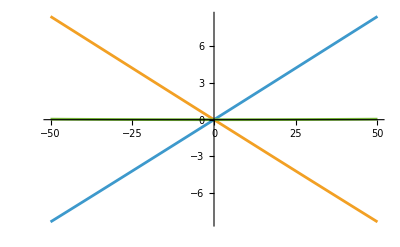

```mathematica
scale={0,1.7892023322662852*^-7,1.789202332266285*^-7,3.57840466453257*^-7};

list={{-50,1.6396882423313547*^-7,1.940182704280965*^-7,3.5798709466123197*^-7},{-45,1.6545209472804627*^-7,1.9250798022527492*^-7,3.579600749533212*^-7},{-40,1.6693842777243004*^-7,1.9099713530769193*^-7,3.5793556308012194*^-7},{-35,1.6842767301015048*^-7,1.894859997712697*^-7,3.5791367278142017*^-7},{-30,1.699196751076696*^-7,1.8797482817581137*^-7,3.57894503283481*^-7},{-25,1.7141427377039268*^-7,1.8646386628475399*^-7,3.5787814005514666*^-7},{-20,1.7291130351980098*^-7,1.8495335137738638*^-7,3.5786465489718735*^-7},{-15,1.744105935440324*^-7,1.8344351268440632*^-7,3.578541062284387*^-7},{-10,1.7591196751698916*^-7,1.8193457176664799*^-7,3.5784653928363717*^-7},{-5,1.774152434002017*^-7,1.8042674286543555*^-7,3.5784198626563725*^-7},{0,1.7892023322662876*^-7,1.7892023322662874*^-7,3.578404664532575*^-7},{5,1.8042674286543555*^-7,1.7741524340020167*^-7,3.578419862656372*^-7},{10,1.8193457176664799*^-7,1.759119675169891*^-7,3.5784653928363707*^-7},{15,1.8344351268440632*^-7,1.7441059354403229*^-7,3.578541062284386*^-7},{20,1.8495335137738646*^-7,1.7291130351980103*^-7,3.5786465489718746*^-7},{25,1.8646386628475414*^-7,1.7141427377039273*^-7,3.578781400551469*^-7},{30,1.8797482817581137*^-7,1.6991967510766965*^-7,3.5789450328348103*^-7},{35,1.894859997712697*^-7,1.6842767301015043*^-7,3.579136727814201*^-7},{40,1.90997135307692*^-7,1.6693842777243004*^-7,3.5793556308012205*^-7},{45,1.9250798022527482*^-7,1.6545209472804633*^-7,3.5796007495332114*^-7},{50,1.9401827042809636*^-7,1.6396882423313542*^-7,3.579870946612318*^-7}};
len=Length[list];mult=10^2;
dat11=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat12=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt1=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat11,dat12,datt1}]
```

### set 2

```mathematica
mu=0.03;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/2;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

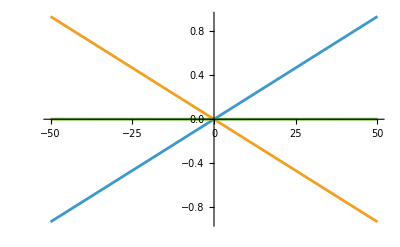

```mathematica
scale={0,1.7892023322662844*^-7,1.7892023322662844*^-7,3.578404664532569*^-7};

list={{-50,1.7724812461709913*^-7,1.8059421799287627*^-7,3.578423426099754*^-7},{-45,1.774152434002017*^-7,1.8042674286543553*^-7,3.578419862656372*^-7},{-40,1.7758238334935736*^-7,1.8025928403198597*^-7,3.5784166738134333*^-7},{-35,1.777495442021099*^-7,1.8009184177161496*^-7,3.5784138597372486*^-7},{-30,1.7791672569505972*^-7,1.799244163623955*^-7,3.5784114205745524*^-7},{-25,1.7808392756385993*^-7,1.7975700808138993*^-7,3.5784093564524983*^-7},{-20,1.782511495432268*^-7,1.7958961720467767*^-7,3.578407667479045*^-7},{-15,1.7841839136689996*^-7,1.7942224400727825*^-7,3.578406353741782*^-7},{-10,1.785856527676131*^-7,1.792548887632389*^-7,3.57840541530852*^-7},{-5,1.7875293347723862*^-7,1.790875517456619*^-7,3.578404852229005*^-7},{0,1.7892023322662874*^-7,1.7892023322662874*^-7,3.5784046645325747*^-7},{5,1.790875517456619*^-7,1.7875293347723867*^-7,3.578404852229006*^-7},{10,1.792548887632389*^-7,1.7858565276761304*^-7,3.5784054153085194*^-7},{15,1.794222440072783*^-7,1.7841839136689996*^-7,3.578406353741783*^-7},{20,1.7958961720467762*^-7,1.7825114954322678*^-7,3.578407667479044*^-7},{25,1.7975700808138977*^-7,1.7808392756385985*^-7,3.578409356452496*^-7},{30,1.799244163623954*^-7,1.779167256950597*^-7,3.578411420574551*^-7},{35,1.800918417716149*^-7,1.777495442021099*^-7,3.578413859737248*^-7},{40,1.8025928403198592*^-7,1.7758238334935738*^-7,3.578416673813433*^-7},{45,1.8042674286543547*^-7,1.774152434002017*^-7,3.578419862656372*^-7},{50,1.8059421799287622*^-7,1.7724812461709913*^-7,3.578423426099754*^-7}};
len=Length[list];mult=10^2;
dat21=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat22=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt2=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat21,dat22,datt2}]
```

### set 3

```mathematica
mu=0.05;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/2;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

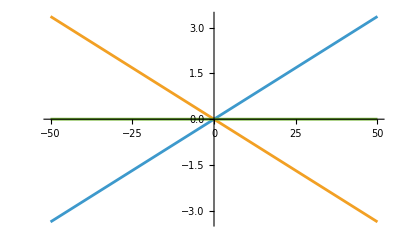

```mathematica
scale={0,1.7892023322662852*^-7,1.789202332266285*^-7,3.57840466453257*^-7};

list={{-50,1.783180439063527*^-7,1.7952266578884836*^-7,3.578407096952011*^-7},{-45,1.7837825153371096*^-7,1.7946241194762703*^-7,3.57840663481338*^-7},{-40,1.7843846170659253*^-7,1.7940216042466251*^-7,3.57840622131255*^-7},{-35,1.784986744125098*^-7,1.7934191123272046*^-7,3.5784058564523024*^-7},{-30,1.7855888963896012*^-7,1.792816643845505*^-7,3.578405540235106*^-7},{-25,1.7861910737342393*^-7,1.7922141989288575*^-7,3.578405272663097*^-7},{-20,1.7867932760336574*^-7,1.7916117777044238*^-7,3.578405053738081*^-7},{-15,1.7873955031623348*^-7,1.7910093802991998*^-7,3.5784048834615346*^-7},{-10,1.7879977549945898*^-7,1.7904070068400186*^-7,3.5784047618346084*^-7},{-5,1.7886000314045772*^-7,1.7898046574535466*^-7,3.578404688858124*^-7},{0,1.789202332266287*^-7,1.789202332266287*^-7,3.578404664532574*^-7},{5,1.789804657453547*^-7,1.7886000314045772*^-7,3.5784046888581243*^-7},{10,1.7904070068400186*^-7,1.7879977549945898*^-7,3.5784047618346084*^-7},{15,1.7910093802992*^-7,1.7873955031623354*^-7,3.5784048834615357*^-7},{20,1.7916117777044233*^-7,1.786793276033657*^-7,3.5784050537380804*^-7},{25,1.7922141989288572*^-7,1.7861910737342388*^-7,3.5784052726630963*^-7},{30,1.7928166438455042*^-7,1.7855888963895996*^-7,3.578405540235104*^-7},{35,1.7934191123272046*^-7,1.7849867441250983*^-7,3.578405856452303*^-7},{40,1.7940216042466251*^-7,1.784384617065925*^-7,3.57840622131255*^-7},{45,1.7946241194762722*^-7,1.7837825153371114*^-7,3.5784066348133833*^-7},{50,1.7952266578884842*^-7,1.7831804390635272*^-7,3.5784070969520114*^-7}};len=Length[list];mult=10^3;
dat31=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat32=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt3=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat31,dat32,datt3}]
```

### set 4

```mathematica
mu=0.01;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/100;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

{0,2.65723×10^-7,2.65723×10^-7,5.31446×10^-7,(3.05032×10^-20
-0.000182454
-9.55758×10^-22
-1.05468×10^-20
-0.000182454
-9.55758×10^-22),5,1.34552×10^-15}

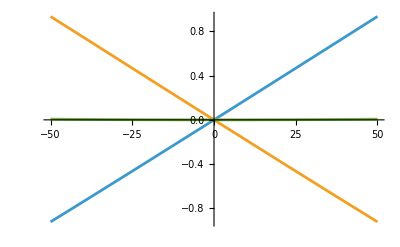

```mathematica
scale={0,2.657231186534087*^-7,2.6572311865340863*^-7,5.314462373068174*^-7};

list={{-50,2.4123510813865336*^-7,2.905350600671981*^-7,5.317701682058515*^-7},{-45,2.436585371009133*^-7,2.8805147422072407*^-7,5.317100113216374*^-7},{-40,2.460885048077216*^-7,2.855671251875921*^-7,5.316556299953137*^-7},{-35,2.4852468704793657*^-7,2.8308252540998143*^-7,5.31607212457918*^-7},{-30,2.509667523279941*^-7,2.805981706340569*^-7,5.31564922962051*^-7},{-25,2.5341436154708723*^-7,2.781145414383807*^-7,5.315289029854679*^-7},{-20,2.558671676365003*^-7,2.75632103757278*^-7,5.314992713937783*^-7},{-15,2.583248151829812*^-7,2.7315130972222875*^-7,5.314761249052099*^-7},{-10,2.6078694002733117*^-7,2.706725983869591*^-7,5.314595384142903*^-7},{-5,2.632531688373931*^-7,2.6819639640351975*^-7,5.314495652409129*^-7},{0,2.6572311865340906*^-7,2.65723118653409*^-7,5.31446237306818*^-7},{5,2.6819639640351975*^-7,2.632531688373931*^-7,5.314495652409129*^-7},{10,2.706725983869591*^-7,2.607869400273312*^-7,5.314595384142903*^-7},{15,2.7315130972222875*^-7,2.583248151829811*^-7,5.314761249052098*^-7},{20,2.7563210375727794*^-7,2.5586716763650034*^-7,5.314992713937783*^-7},{25,2.781145414383809*^-7,2.5341436154708734*^-7,5.315289029854682*^-7},{30,2.8059817063405693*^-7,2.509667523279942*^-7,5.315649229620511*^-7},{35,2.8308252540998143*^-7,2.4852468704793657*^-7,5.31607212457918*^-7},{40,2.855671251875921*^-7,2.460885048077216*^-7,5.316556299953137*^-7},{45,2.88051474220724*^-7,2.4365853710091353*^-7,5.317100113216376*^-7},{50,2.905350600671982*^-7,2.4123510813865315*^-7,5.317701682058514*^-7}};

len=Length[list];mult=10^1;
dat41=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat42=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt4=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat41,dat42,datt4}]
```

### set 5

```mathematica
mu=0.03;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/100;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

{0,2.65723×10^-7,2.65723×10^-7,5.31446×10^-7,(5.97083×10^-20
-0.000182454
4.11711×10^-21
-1.34742×10^-20
-0.000182454
4.11711×10^-21),5,1.34552×10^-15}

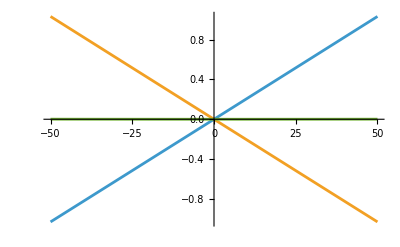

```mathematica
scale={0,2.657231186534086*^-7,2.6572311865340853*^-7,5.314462373068172*^-7};
list={{-50,2.629789525708633*^-7,2.684713930401417*^-7,5.31450345611005*^-7},{-45,2.63253168837393*^-7,2.681963964035196*^-7,5.314495652409126*^-7},{-40,2.6352743105253873*^-7,2.6792143587989957*^-7,5.314488669324384*^-7},{-35,2.6380173868344174*^-7,2.676465120296784*^-7,5.314482507131201*^-7},{-30,2.640760911956946*^-7,2.6737162541155987*^-7,5.314477166072544*^-7},{-25,2.643504880533322*^-7,2.6709677658256343*^-7,5.314472646358956*^-7},{-20,2.6462492871882464*^-7,2.668219660980891*^-7,5.314468948169137*^-7},{-15,2.648994126531361*^-7,2.6654719451168255*^-7,5.314466071648186*^-7},{-10,2.651739393153974*^-7,2.662724623754526*^-7,5.3144640169085*^-7},{-5,2.654485081634498*^-7,2.6599777023978114*^-7,5.314462784032309*^-7},{0,2.65723118653409*^-7,2.65723118653409*^-7,5.31446237306818*^-7},{5,2.659977702397812*^-7,2.6544850816344986*^-7,5.31446278403231*^-7},{10,2.662724623754526*^-7,2.651739393153974*^-7,5.3144640169085*^-7},{15,2.6654719451168244*^-7,2.648994126531361*^-7,5.314466071648185*^-7},{20,2.6682196609808905*^-7,2.6462492871882464*^-7,5.314468948169137*^-7},{25,2.6709677658256333*^-7,2.643504880533321*^-7,5.314472646358954*^-7},{30,2.673716254115597*^-7,2.6407609119569444*^-7,5.314477166072542*^-7},{35,2.676465120296784*^-7,2.6380173868344163*^-7,5.3144825071312*^-7},{40,2.679214358798996*^-7,2.6352743105253873*^-7,5.314488669324384*^-7},{45,2.681963964035195*^-7,2.632531688373931*^-7,5.314495652409126*^-7},{50,2.6847139304014157*^-7,2.629789525708633*^-7,5.314503456110049*^-7}};
len=Length[list];mult=10^2;
dat51=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat52=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt5=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat51,dat52,datt5}]
```

### set 6

```mathematica
mu=0.05;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val);inter=ampli/100;
datset=Table[Quiet[sig[B,mu,v0val,{inter,ampli}]],{B,-50,50,100/20}]
Quiet[sig0[mu,v0val,{inter,ampli}]]
```

{0,2.65723×10^-7,2.65723×10^-7,5.31446×10^-7,(2.06275×10^-20
-0.000182454
-6.34944×10^-22
-3.54299×10^-20
-0.000182454
-6.34944×10^-22),5,1.34454×10^-15}

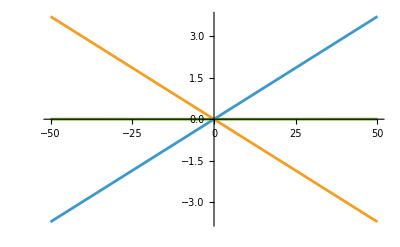

```mathematica
scale={0,2.657231186534086*^-7,2.657231186534086*^-7,5.314462373068172*^-7};

list={{-50,2.6473471713061473*^-7,2.667120527647991*^-7,5.314467698954138*^-7},{-45,2.648335325917223*^-7,2.6661313611534606*^-7,5.314466687070684*^-7},{-40,2.6493235360723976*^-7,2.6651422456150126*^-7,5.31446578168741*^-7},{-35,2.6503118015190766*^-7,2.6641531812898595*^-7,5.314464982808936*^-7},{-30,2.6513001220044054*^-7,2.663164168434934*^-7,5.31446429043934*^-7},{-25,2.652288497275258*^-7,2.662175207306903*^-7,5.314463704582161*^-7},{-20,2.653276927078235*^-7,2.661186298162157*^-7,5.314463225240392*^-7},{-15,2.6542654111596767*^-7,2.660197441256798*^-7,5.314462852416475*^-7},{-10,2.6552539492656494*^-7,2.659208636846673*^-7,5.314462586112323*^-7},{-5,2.656242541141945*^-7,2.658219885187339*^-7,5.314462426329284*^-7},{0,2.6572311865340906*^-7,2.6572311865340906*^-7,5.314462373068181*^-7},{5,2.658219885187338*^-7,2.656242541141944*^-7,5.314462426329281*^-7},{10,2.659208636846673*^-7,2.6552539492656504*^-7,5.314462586112323*^-7},{15,2.6601974412568*^-7,2.654265411159679*^-7,5.314462852416479*^-7},{20,2.661186298162157*^-7,2.6532769270782356*^-7,5.314463225240393*^-7},{25,2.662175207306905*^-7,2.6522884972752566*^-7,5.314463704582162*^-7},{30,2.6631641684349345*^-7,2.6513001220044043*^-7,5.314464290439339*^-7},{35,2.6641531812898595*^-7,2.650311801519077*^-7,5.314464982808937*^-7},{40,2.665142245615013*^-7,2.649323536072396*^-7,5.314465781687409*^-7},{45,2.6661313611534606*^-7,2.648335325917225*^-7,5.314466687070686*^-7},{50,2.667120527647992*^-7,2.6473471713061473*^-7,5.314467698954139*^-7}};

len=Length[list];mult=10^3;
dat61=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)mult},{i,1,len}];
dat62=Table[{list[[i,1]],(list[[i,3]]/scale[[3]]-1)mult},{i,1,len}];
datt6=Table[{list[[i,1]],(list[[i,4]]/scale[[4]]-1)mult},{i,1,len}];
ListLinePlot[{dat61,dat62,datt6}]
```

## Final Plots

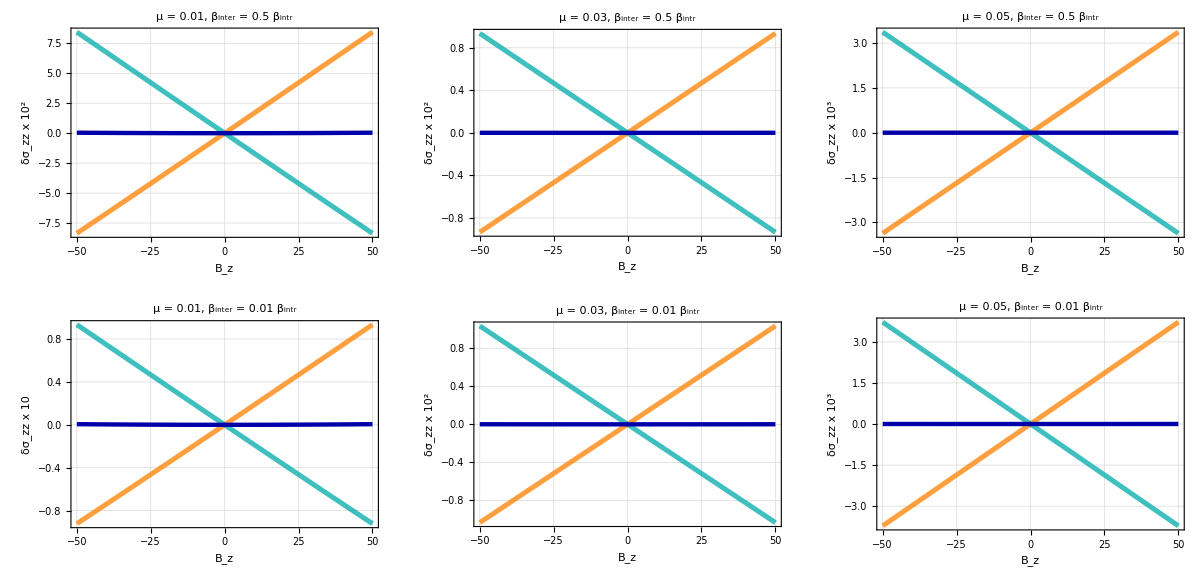

```mathematica
thk=0.007;
style={(**)Directive[Orange,Thickness[0.008],Opacity[0.75]],(**)Directive[Darker[Cyan],Thickness[0.008],Opacity[0.75]](***),Directive[Darker[Blue],Thickness[0.007]]};
(********)
mu=0.01;
p1=ListLinePlot[{dat11,dat12,datt1},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10^2"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.01,  β_inter = 0.5 β_intr",Bold,Brown,18]];
p4=ListLinePlot[{dat41,dat42,datt4},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.01,  β_inter = 0.01 β_intr",Bold,Brown,18]];

mu=0.03;
(****************)
p2=ListLinePlot[{dat21,dat22,datt2},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10^2"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.03,  β_inter = 0.5 β_intr",Bold,Brown,18]];
p5=ListLinePlot[{dat51,dat52,datt5},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10^2"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.03,  β_inter = 0.01 β_intr",Bold,Brown,18]];
(*****************)
mu=0.05;
p3=ListLinePlot[{dat31,dat32,datt3},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10^3"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.05,  β_inter = 0.5 β_intr",Bold,Brown,18]];
p6=ListLinePlot[{dat61,dat62,datt6},PlotRange->{{-50,50},Automatic},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz x 10^3"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLabel->Style["μ = 0.05,  β_inter = 0.01 β_intr",Bold,Brown,18]];

leg=LineLegend[style,{"χ = 1","χ = -1","sum of 2 nodes"},LabelStyle->{FontFamily->"Times",18,Bold,Darker[Gray]},LegendLayout->{"Row",1}];

p=Legended[GraphicsGrid[{{p1,p2,p3},{p4,p5,p6}},Spacings->{10,10},ImageSize->1200],Placed[leg,Below]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["sigz-2node.pdf",Rasterize[p,Background->None],ImageResolution->100];
```